```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA"}]]
```

Successfully patched FeynArts.

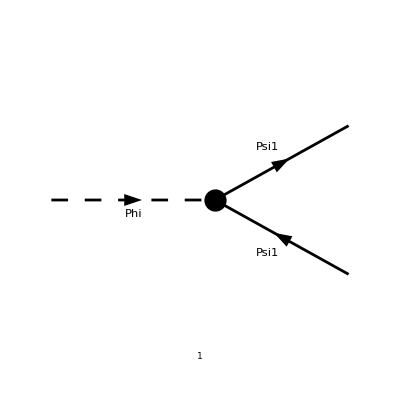

```mathematica
DecayDiags = InsertFields[CreateTopologies[0, 1 -> 2, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->{F[1],-F[1]}, InsertionLevel->{Particles},Model -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}]];
Paint[DecayDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{4,1},ImageSize->{400,100}];
```

```mathematica
FCClearScalarProducts;
Pair[Momentum[k1,D],Momentum[k2,D]]=ECM^2/2-mPsi1^2;
```

```mathematica
AmpDecay=(Contract/@FCFAConvert[CreateFeynAmp[DecayDiags],IncomingMomenta->{p},OutgoingMomenta->{k1,k2},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings])/.{Y1r->Re[Y1],Y1i->Im[Y1]}//Total
```

ⅈ (φ(k1,mPsi1)).(Im(Y1)-ⅈ Re(Y1)).(φ(-k2,mPsi1))

```mathematica
AmpSquared=AmpDecay(ComplexConjugate[AmpDecay])//FermionSpinSum[#]&//DiracSimplify//FullSimplify
```

2 Y1 Conjugate[Y1] (ECM^2-4 mPsi1^2)

```mathematica
ImLoop=1/2(√(ECM^2-4 mPsi1^2))/(32 π^2 ECM)4π AmpSquared
```

(Y1 Conjugate[Y1] (ECM^2-4 mPsi1^2)^(3/2))/(8 π ECM)

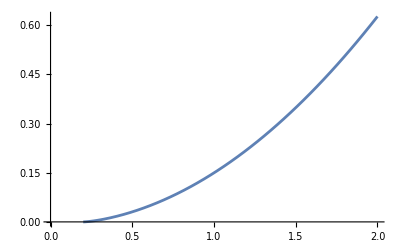

```mathematica
Plot[ImLoop/.{mPhi->1,mPsi1->0.1,Y1->2},{ECM,0,2},PlotRange->Full,MaxRecursion->10]
```